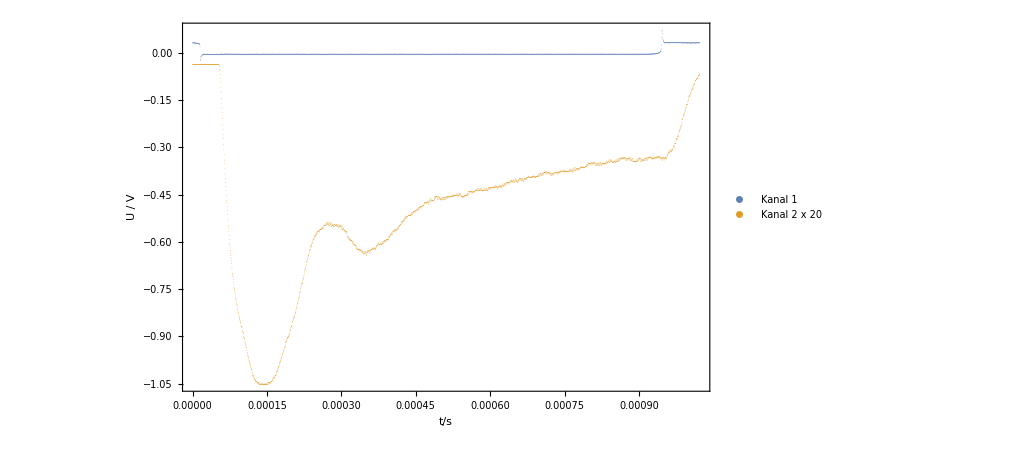

```mathematica
path = "./part4/04-+5.tab";
ch1zoom = 1;
ch2zoom = 20;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

```mathematica
MaxPos={{{0.0001227,-0.4225},{0.0004244,-0.6449}},{{0.000144,-0.5034},{0.0004047,-0.5907}},{{0.0001985,-0.4231},{0.000567,-0.4472}},{{0.0002728,-0.5399},{0.0004896,-0.4622}},{{0.0001682,-0.5911},{0.0004502,-0.5425}},{{0.0001394,-0.6847},{0.000429,-0.5476}}};
Maxdiff=#[[2,1]]-#[[1,1]]&/@MaxPos
MaxNum={3,2,2,1,2,3};
T=10^6 Maxdiff/MaxNum
Deg={-10,-7.5,-5,5,7.5,10};
```

{0.0003017,0.0002607,0.0003685,0.0002168,0.000282,0.0002896}

{100.567,130.35,184.25,216.8,141.,96.5333}

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.00100402 | 0.0000184795 | 54.3315 | 6.87011×10^-7
b | 0.162489 | 0.143094 | 1.13554 | 0.319572

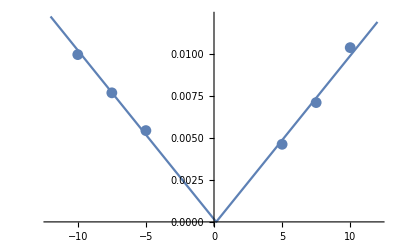

```mathematica
data=Transpose[{Deg,1/T}];
nlm=NonlinearModelFit[data,a Abs[x-b],{a,b},x];
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,-12,12}],ListPlot[data,PlotRange->{0,0.012}]]
```